# Graph Cartesian Product

### Author

Eric W. Weisstein
August 7, 2023

This notebook downloaded from http://mathworld.wolfram.com/notebooks/GraphTheory/GraphCartesianProduct.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/GraphCartesianProduct.html.

©2023 Wolfram Research, Inc. except for portions noted otherwise

## Special Cases

### P_m□P_n≃ {"Grid", {m, n}}

```mathematica
TextGrid[data=Flatten[Table[{{m,n},"Grid"/.GraphData[c=CanonicalName[ToEntity@GraphCartesianProduct[PathGraph[Range[m]],PathGraph[Range[n]]]],"NotationRules"],c},{n,10},{m,n}],1],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]
```

{1,1} | {1} | SingletonGraph
{1,2} | {2} | {Path,2}
{2,2} | {2,2} | SquareGraph
{1,3} | {3} | {Path,3}
{2,3} | {2,3} | DominoGraph
{3,3} | {3,3} | {Grid,{3,3}}
{1,4} | {4} | {Path,4}
{2,4} | {2,4} | {Ladder,4}
{3,4} | {3,4} | {Grid,{3,4}}
{4,4} | {4,4} | {Grid,{4,4}}
{1,5} | {5} | {Path,5}
{2,5} | {2,5} | {Ladder,5}
{3,5} | {3,5} | {Grid,{3,5}}
{4,5} | {4,5} | {Grid,{4,5}}
{5,5} | {5,5} | {Grid,{5,5}}
{1,6} | {6} | {Path,6}
{2,6} | {2,6} | {Ladder,6}
{3,6} | {3,6} | {Grid,{3,6}}
{4,6} | {4,6} | {Grid,{4,6}}
{5,6} | {5,6} | {Grid,{5,6}}
{6,6} | {6,6} | {Grid,{6,6}}
{1,7} | {7} | {Path,7}
{2,7} | {2,7} | {Ladder,7}
{3,7} | {3,7} | {Grid,{3,7}}
{4,7} | {4,7} | {Grid,{4,7}}
{5,7} | {5,7} | {Grid,{5,7}}
{6,7} | {6,7} | {Grid,{6,7}}
{7,7} | {7,7} | {Grid,{7,7}}
{1,8} | {8} | {Path,8}
{2,8} | {2,8} | {Ladder,8}
{3,8} | {3,8} | {Grid,{3,8}}
{4,8} | {4,8} | {Grid,{4,8}}
{5,8} | {5,8} | {Grid,{5,8}}
{6,8} | {6,8} | {Grid,{6,8}}
{7,8} | {7,8} | {Grid,{7,8}}
{8,8} | {8,8} | {Grid,{8,8}}
{1,9} | {9} | {Path,9}
{2,9} | {2,9} | {Ladder,9}
{3,9} | {3,9} | {Grid,{3,9}}
{4,9} | {4,9} | {Grid,{4,9}}
{5,9} | {5,9} | {Grid,{5,9}}
{6,9} | {6,9} | {Grid,{6,9}}
{7,9} | {7,9} | {Grid,{7,9}}
{8,9} | {8,9} | {Grid,{8,9}}
{9,9} | {9,9} | {Grid,{9,9}}
{1,10} | {10} | {Path,10}
{2,10} | {2,10} | {Ladder,10}
{3,10} | {3,10} | {Grid,{3,10}}
{4,10} | {4,10} | {Grid,{4,10}}
{5,10} | {5,10} | {Grid,{5,10}}
{6,10} | {6,10} | {Grid,{6,10}}
{7,10} | {7,10} | {Grid,{7,10}}
{8,10} | {8,10} | {Grid,{8,10}}
{9,10} | {9,10} | {Grid,{9,10}}
{10,10} | {10,10} | {Grid,{10,10}}

```mathematica
Cases[data,{x_,"Grid",y_}:>(y->x)]
```

{}

### P_m□P_2≃ {"Ladder",m}

```mathematica
TextGrid[data=Table[{m,"Ladder"/.GraphData[c=CanonicalName[ToEntity@GraphCartesianProduct[PathGraph[Range[m]],PathGraph[Range[2]]]],"NotationRules"],c},{m,20}],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]
```

1 | 1 | {Path,2}
2 | 2 | SquareGraph
3 | 3 | DominoGraph
4 | 4 | {Ladder,4}
5 | 5 | {Ladder,5}
6 | 6 | {Ladder,6}
7 | 7 | {Ladder,7}
8 | 8 | {Ladder,8}
9 | 9 | {Ladder,9}
10 | 10 | {Ladder,10}
11 | 11 | {Ladder,11}
12 | 12 | {Ladder,12}
13 | 13 | {Ladder,13}
14 | 14 | {Ladder,14}
15 | 15 | {Ladder,15}
16 | 16 | {Ladder,16}
17 | 17 | {Ladder,17}
18 | 18 | {Ladder,18}
19 | 19 | {Ladder,19}
20 | 20 | {Ladder,20}

```mathematica
Cases[data,{x_,"Ladder",y_}:>(y->x)]
```

{}

### C_m□P_2≃ {"Prism",m}

```mathematica
TextGrid[data=Table[{m,"Prism"/.GraphData[c=CanonicalName[ToEntity@GraphCartesianProduct[CycleGraph[m],PathGraph[Range[2]]]],"NotationRules"],c},{m,3,20}],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]
```

3 | 3 | {Prism,3}
4 | 4 | CubicalGraph
5 | 5 | {Prism,5}
6 | 6 | {Prism,6}
7 | 7 | {Prism,7}
8 | 8 | {Prism,8}
9 | 9 | {Prism,9}
10 | 10 | {Prism,10}
11 | 11 | {Prism,11}
12 | 12 | {Prism,12}
13 | 13 | {Prism,13}
14 | 14 | {Prism,14}
15 | 15 | {Prism,15}
16 | 16 | {Prism,16}
17 | 17 | {Prism,17}
18 | 18 | {Prism,18}
19 | 19 | {Prism,19}
20 | 20 | {Prism,20}

```mathematica
Cases[data,{x_,"Prism",y_}:>(y->x)]
```

{}

### C_m□P_n≃ {"StackedPrism",{m,n}}

```mathematica
TextGrid[data=DeleteCases[Flatten[Table[{{m,n},"StackedPrism"/.GraphData[c=CanonicalName@ToEntity@GraphCartesianProduct[CycleGraph[m],PathGraph[Range[n]]],"NotationRules"],c},{n,5},{m,3,10}],1],{_,_,_CanonicalName}],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]//Quiet
```

{3,1} | {3,1} | TriangleGraph
{4,1} | {4,1} | SquareGraph
{5,1} | {5,1} | {Cycle,5}
{6,1} | {6,1} | {Cycle,6}
{7,1} | {7,1} | {Cycle,7}
{8,1} | {8,1} | {Cycle,8}
{9,1} | {9,1} | {Cycle,9}
{10,1} | {10,1} | {Cycle,10}
{3,2} | {3,2} | {Prism,3}
{4,2} | {4,2} | CubicalGraph
{5,2} | {5,2} | {Prism,5}
{6,2} | {6,2} | {Prism,6}
{7,2} | {7,2} | {Prism,7}
{8,2} | {8,2} | {Prism,8}
{9,2} | {9,2} | {Prism,9}
{10,2} | {10,2} | {Prism,10}
{3,3} | {3,3} | {StackedPrism,{3,3}}
{4,3} | {4,3} | {Grid,{2,2,3}}
{5,3} | {5,3} | {StackedPrism,{5,3}}
{6,3} | {6,3} | {StackedPrism,{6,3}}
{7,3} | {7,3} | {StackedPrism,{7,3}}
{8,3} | {8,3} | {StackedPrism,{8,3}}
{3,4} | {3,4} | {StackedPrism,{3,4}}
{4,4} | {4,4} | {Grid,{2,2,4}}
{5,4} | {5,4} | {StackedPrism,{5,4}}
{6,4} | {6,4} | {StackedPrism,{6,4}}
{7,4} | {7,4} | {StackedPrism,{7,4}}
{8,4} | {8,4} | {StackedPrism,{8,4}}
{3,5} | {3,5} | {StackedPrism,{3,5}}
{4,5} | {4,5} | {Grid,{2,2,5}}
{5,5} | {5,5} | {StackedPrism,{5,5}}
{6,5} | {6,5} | {StackedPrism,{6,5}}
{7,5} | {7,5} | {StackedPrism,{7,5}}
{8,5} | {8,5} | {StackedPrism,{8,5}}

```mathematica
Cases[data,{x_,"StackedPrism",y_}:>(y->x)]
```

{}

### C_m□C_n≃ {"TorusGrid",{m,n}}

```mathematica
TextGrid[data=Flatten[Table[{{m,n},"TorusGrid"/.GraphData[c=CanonicalName[ToEntity@GraphCartesianProduct[CycleGraph[m],CycleGraph[n]]],"NotationRules"],c},{n,3,10},{m,3,10}],1],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]
```

{3,3} | {3,3} | {GeneralizedQuadrangle,{2,1}}
{4,3} | {3,4} | {Circulant,{12,{3,4}}}
{5,3} | {3,5} | {Circulant,{15,{3,5}}}
{6,3} | {3,6} | {QuarticTransitive,65}
{7,3} | {3,7} | {Circulant,{21,{3,7}}}
{8,3} | {3,8} | {Circulant,{24,{3,8}}}
{9,3} | {3,9} | {TorusGrid,{3,9}}
{10,3} | {3,10} | {Circulant,{30,{3,10}}}
{3,4} | {3,4} | {Circulant,{12,{3,4}}}
{4,4} | {4,4} | TesseractGraph
{5,4} | {4,5} | {Circulant,{20,{4,5}}}
{6,4} | {4,6} | {TorusGrid,{4,6}}
{7,4} | {4,7} | {Circulant,{28,{4,7}}}
{8,4} | {4,8} | {TorusGrid,{4,8}}
{9,4} | {4,9} | {Circulant,{36,{4,9}}}
{10,4} | {4,10} | {TorusGrid,{4,10}}
{3,5} | {3,5} | {Circulant,{15,{3,5}}}
{4,5} | {4,5} | {Circulant,{20,{4,5}}}
{5,5} | {5,5} | {TorusGrid,{5,5}}
{6,5} | {5,6} | {Circulant,{30,{5,6}}}
{7,5} | {5,7} | {Circulant,{35,{5,7}}}
{8,5} | {5,8} | {Circulant,{40,{5,8}}}
{9,5} | {5,9} | {Circulant,{45,{5,9}}}
{10,5} | {5,10} | {TorusGrid,{5,10}}
{3,6} | {3,6} | {QuarticTransitive,65}
{4,6} | {4,6} | {TorusGrid,{4,6}}
{5,6} | {5,6} | {Circulant,{30,{5,6}}}
{6,6} | {6,6} | {TorusGrid,{6,6}}
{7,6} | {6,7} | {Circulant,{42,{6,7}}}
{8,6} | {6,8} | {TorusGrid,{6,8}}
{9,6} | {6,9} | {TorusGrid,{6,9}}
{10,6} | {6,10} | {TorusGrid,{6,10}}
{3,7} | {3,7} | {Circulant,{21,{3,7}}}
{4,7} | {4,7} | {Circulant,{28,{4,7}}}
{5,7} | {5,7} | {Circulant,{35,{5,7}}}
{6,7} | {6,7} | {Circulant,{42,{6,7}}}
{7,7} | {7,7} | {TorusGrid,{7,7}}
{8,7} | {7,8} | {Circulant,{56,{7,8}}}
{9,7} | {7,9} | {Circulant,{63,{7,9}}}
{10,7} | {7,10} | {Circulant,{70,{7,10}}}
{3,8} | {3,8} | {Circulant,{24,{3,8}}}
{4,8} | {4,8} | {TorusGrid,{4,8}}
{5,8} | {5,8} | {Circulant,{40,{5,8}}}
{6,8} | {6,8} | {TorusGrid,{6,8}}
{7,8} | {7,8} | {Circulant,{56,{7,8}}}
{8,8} | {8,8} | {TorusGrid,{8,8}}
{9,8} | {8,9} | {Circulant,{72,{8,9}}}
{10,8} | {8,10} | {TorusGrid,{8,10}}
{3,9} | {3,9} | {TorusGrid,{3,9}}
{4,9} | {4,9} | {Circulant,{36,{4,9}}}
{5,9} | {5,9} | {Circulant,{45,{5,9}}}
{6,9} | {6,9} | {TorusGrid,{6,9}}
{7,9} | {7,9} | {Circulant,{63,{7,9}}}
{8,9} | {8,9} | {Circulant,{72,{8,9}}}
{9,9} | {9,9} | {TorusGrid,{9,9}}
{10,9} | {9,10} | {Circulant,{90,{9,10}}}
{3,10} | {3,10} | {Circulant,{30,{3,10}}}
{4,10} | {4,10} | {TorusGrid,{4,10}}
{5,10} | {5,10} | {TorusGrid,{5,10}}
{6,10} | {6,10} | {TorusGrid,{6,10}}
{7,10} | {7,10} | {Circulant,{70,{7,10}}}
{8,10} | {8,10} | {TorusGrid,{8,10}}
{9,10} | {9,10} | {Circulant,{90,{9,10}}}
{10,10} | {10,10} | {TorusGrid,{10,10}}

```mathematica
Cases[data,{x_,"TorusGrid",y_}:>(y->x)]
```

{}

### S_(m+1)□P_2≃ {"Book",m}

```mathematica
TextGrid[data=Table[{m,"Book"/.GraphData[c=CanonicalName[ToEntity@GraphCartesianProduct[StarGraph[m+1],PathGraph[{1,2}]]],"NotationRules"],c},{m,10}],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]
```

1 | 1 | SquareGraph
2 | 2 | DominoGraph
3 | 3 | {Book,3}
4 | 4 | {Book,4}
5 | 5 | {Book,5}
6 | 6 | {Book,6}
7 | 7 | {Book,7}
8 | 8 | {Book,8}
9 | 9 | {Book,9}
10 | 10 | {Book,10}

```mathematica
Cases[data,{x_,"Book",y_}:>(y->x)]
```

{}

### S_(m+1)□P_n≃ {"StackedBook",{m,n}}

```mathematica
TextGrid[data=Flatten[Table[{{m,n},"StackedBook"/.GraphData[c=CanonicalName[ToEntity@GraphCartesianProduct[StarGraph[m+1],PathGraph[Range[n]]]],"NotationRules"],c},{n,10},{m,10}],1],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]
```

{1,1} | {1,1} | {Path,2}
{2,1} | {2,1} | {Path,3}
{3,1} | {3,1} | ClawGraph
{4,1} | {4,1} | {Star,5}
{5,1} | {5,1} | {Star,6}
{6,1} | {6,1} | {Star,7}
{7,1} | {7,1} | {Star,8}
{8,1} | {8,1} | {Star,9}
{9,1} | {9,1} | {Star,10}
{10,1} | {10,1} | {Star,11}
{1,2} | {1,2} | SquareGraph
{2,2} | {2,2} | DominoGraph
{3,2} | {3,2} | {Book,3}
{4,2} | {4,2} | {Book,4}
{5,2} | {5,2} | {Book,5}
{6,2} | {6,2} | {Book,6}
{7,2} | {7,2} | {Book,7}
{8,2} | {8,2} | {Book,8}
{9,2} | {9,2} | {Book,9}
{10,2} | {10,2} | {Book,10}
{1,3} | {2,2} | DominoGraph
{2,3} | {2,3} | {Grid,{3,3}}
{3,3} | {3,3} | {StackedBook,{3,3}}
{4,3} | {4,3} | {StackedBook,{4,3}}
{5,3} | {5,3} | {StackedBook,{5,3}}
{6,3} | {6,3} | {StackedBook,{6,3}}
{7,3} | {7,3} | {StackedBook,{7,3}}
{8,3} | {8,3} | {StackedBook,{8,3}}
{9,3} | {9,3} | {StackedBook,{9,3}}
{10,3} | {10,3} | {StackedBook,{10,3}}
{1,4} | {1,4} | {Ladder,4}
{2,4} | {2,4} | {Grid,{3,4}}
{3,4} | {3,4} | {StackedBook,{3,4}}
{4,4} | {4,4} | {StackedBook,{4,4}}
{5,4} | {5,4} | {StackedBook,{5,4}}
{6,4} | {6,4} | {StackedBook,{6,4}}
{7,4} | {7,4} | {StackedBook,{7,4}}
{8,4} | {8,4} | {StackedBook,{8,4}}
{9,4} | {9,4} | {StackedBook,{9,4}}
{10,4} | {10,4} | {StackedBook,{10,4}}
{1,5} | {1,5} | {Ladder,5}
{2,5} | {2,5} | {Grid,{3,5}}
{3,5} | {3,5} | {StackedBook,{3,5}}
{4,5} | {4,5} | {StackedBook,{4,5}}
{5,5} | {5,5} | {StackedBook,{5,5}}
{6,5} | {6,5} | {StackedBook,{6,5}}
{7,5} | {7,5} | {StackedBook,{7,5}}
{8,5} | {8,5} | {StackedBook,{8,5}}
{9,5} | {9,5} | {StackedBook,{9,5}}
{10,5} | {10,5} | {StackedBook,{10,5}}
{1,6} | {1,6} | {Ladder,6}
{2,6} | {2,6} | {Grid,{3,6}}
{3,6} | {3,6} | {StackedBook,{3,6}}
{4,6} | {4,6} | {StackedBook,{4,6}}
{5,6} | {5,6} | {StackedBook,{5,6}}
{6,6} | {6,6} | {StackedBook,{6,6}}
{7,6} | {7,6} | {StackedBook,{7,6}}
{8,6} | {8,6} | {StackedBook,{8,6}}
{9,6} | {9,6} | {StackedBook,{9,6}}
{10,6} | {10,6} | {StackedBook,{10,6}}
{1,7} | {1,7} | {Ladder,7}
{2,7} | {2,7} | {Grid,{3,7}}
{3,7} | {3,7} | {StackedBook,{3,7}}
{4,7} | {4,7} | {StackedBook,{4,7}}
{5,7} | {5,7} | {StackedBook,{5,7}}
{6,7} | {6,7} | {StackedBook,{6,7}}
{7,7} | {7,7} | {StackedBook,{7,7}}
{8,7} | {8,7} | {StackedBook,{8,7}}
{9,7} | {9,7} | {StackedBook,{9,7}}
{10,7} | {10,7} | {StackedBook,{10,7}}
{1,8} | {1,8} | {Ladder,8}
{2,8} | {2,8} | {Grid,{3,8}}
{3,8} | {3,8} | {StackedBook,{3,8}}
{4,8} | {4,8} | {StackedBook,{4,8}}
{5,8} | {5,8} | {StackedBook,{5,8}}
{6,8} | {6,8} | {StackedBook,{6,8}}
{7,8} | {7,8} | {StackedBook,{7,8}}
{8,8} | {8,8} | {StackedBook,{8,8}}
{9,8} | {9,8} | {StackedBook,{9,8}}
{10,8} | {10,8} | {StackedBook,{10,8}}
{1,9} | {1,9} | {Ladder,9}
{2,9} | {2,9} | {Grid,{3,9}}
{3,9} | {3,9} | {StackedBook,{3,9}}
{4,9} | {4,9} | {StackedBook,{4,9}}
{5,9} | {5,9} | {StackedBook,{5,9}}
{6,9} | {6,9} | {StackedBook,{6,9}}
{7,9} | {7,9} | {StackedBook,{7,9}}
{8,9} | {8,9} | {StackedBook,{8,9}}
{9,9} | {9,9} | {StackedBook,{9,9}}
{10,9} | {10,9} | {StackedBook,{10,9}}
{1,10} | {1,10} | {Ladder,10}
{2,10} | {2,10} | {Grid,{3,10}}
{3,10} | {3,10} | {StackedBook,{3,10}}
{4,10} | {4,10} | {StackedBook,{4,10}}
{5,10} | {5,10} | {StackedBook,{5,10}}
{6,10} | {6,10} | {StackedBook,{6,10}}
{7,10} | {7,10} | {StackedBook,{7,10}}
{8,10} | {8,10} | {StackedBook,{8,10}}
{9,10} | {9,10} | {StackedBook,{9,10}}
{10,10} | {10,10} | {StackedBook,{10,10}}

```mathematica
Cases[data,{x_,"StackedBook",y_}:>(y->x)]
```

{}

### K_m□K_n≃ {"Rook", {m, n}}

```mathematica
TextGrid[data=Flatten[Table[{{m,n},"Rook"/.GraphData[c=CanonicalName[ToEntity@GraphCartesianProduct[System`CompleteGraph[m],System`CompleteGraph[n]]],"NotationRules"],c},{n,10},{m,n}],1],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]
```

{1,1} | {1,1} | SingletonGraph
{1,2} | {1,2} | {Path,2}
{2,2} | {2,2} | SquareGraph
{1,3} | {1,3} | TriangleGraph
{2,3} | {2,3} | {Prism,3}
{3,3} | {3,3} | {GeneralizedQuadrangle,{2,1}}
{1,4} | {1,4} | TetrahedralGraph
{2,4} | {2,4} | {Rook,{2,4}}
{3,4} | {3,4} | {Circulant,{12,{3,4,6}}}
{4,4} | {4,4} | {Rook,{4,4}}
{1,5} | {1,5} | PentatopeGraph
{2,5} | {2,5} | {Circulant,{10,{2,4,5}}}
{3,5} | {3,5} | {Circulant,{15,{3,5,6}}}
{4,5} | {4,5} | {Circulant,{20,{4,5,8,10}}}
{5,5} | {5,5} | {Rook,{5,5}}
{1,6} | {1,6} | {Complete,6}
{2,6} | {2,6} | {Rook,{2,6}}
{3,6} | {3,6} | {Rook,{3,6}}
{4,6} | {4,6} | {Rook,{4,6}}
{5,6} | {5,6} | {Circulant,{30,{5,6,10,12,15}}}
{6,6} | {6,6} | {Rook,{6,6}}
{1,7} | {1,7} | {Complete,7}
{2,7} | {2,7} | {Circulant,{14,{2,4,6,7}}}
{3,7} | {3,7} | {Circulant,{21,{3,6,7,9}}}
{4,7} | {4,7} | {Circulant,{28,{4,7,8,12,14}}}
{5,7} | {5,7} | {Circulant,{35,{5,7,10,14,15}}}
{6,7} | {6,7} | {Circulant,{42,{6,7,12,14,18,21}}}
{7,7} | {7,7} | {Rook,{7,7}}
{1,8} | {1,8} | {Complete,8}
{2,8} | {2,8} | {Rook,{2,8}}
{3,8} | {3,8} | {Circulant,{24,{3,6,8,9,12}}}
{4,8} | {4,8} | {Rook,{4,8}}
{5,8} | {5,8} | {Circulant,{40,{5,8,10,15,16,20}}}
{6,8} | {6,8} | {Rook,{6,8}}
{7,8} | {7,8} | {Circulant,{56,{7,8,14,16,21,24,28}}}
{8,8} | {8,8} | {Rook,{8,8}}
{1,9} | {1,9} | {Complete,9}
{2,9} | {2,9} | {Circulant,{18,{2,4,6,8,9}}}
{3,9} | {3,9} | {Rook,{3,9}}
{4,9} | {4,9} | {Circulant,{36,{4,8,9,12,16,18}}}
{5,9} | {5,9} | {Circulant,{45,{5,9,10,15,18,20}}}
{6,9} | {6,9} | {Rook,{6,9}}
{7,9} | {7,9} | {Circulant,{63,{7,9,14,18,21,27,28}}}
{8,9} | {8,9} | {Circulant,{72,{8,9,16,18,24,27,32,36}}}
{9,9} | {9,9} | {Rook,{9,9}}
{1,10} | {1,10} | {Complete,10}
{2,10} | {2,10} | {Rook,{2,10}}
{3,10} | {3,10} | {Circulant,{30,{3,6,9,10,12,15}}}
{4,10} | {4,10} | {Rook,{4,10}}
{5,10} | {5,10} | {Rook,{5,10}}
{6,10} | {6,10} | {Rook,{6,10}}
{7,10} | {7,10} | {Circulant,{70,{7,10,14,20,21,28,30,35}}}
{8,10} | {8,10} | {Rook,{8,10}}
{9,10} | {9,10} | {Circulant,{90,{9,10,18,20,27,30,36,40,45}}}
{10,10} | {10,10} | {Rook,{10,10}}

```mathematica
Cases[data,{x_,"Rook",y_}:>(y->x)]
```

{}

### P_2□… □P_2 == {"Hypercube", n}

```mathematica
TextGrid[data=Table[{n,"Hypercube"/.GraphData[c=CanonicalName[ToEntity@Nest[GraphCartesianProduct[PathGraph[{1,2}],#]&,System`Graph[{1},{}],n]],"NotationRules"],c},{n,10}],Dividers->All,Alignment->{{Decimal,Decimal,Left}}]
```

1 | 1 | {Path,2}
2 | 2 | SquareGraph
3 | 3 | CubicalGraph
4 | 4 | TesseractGraph
5 | 5 | {Hypercube,5}
6 | 6 | {Hypercube,6}
7 | 7 | {Hypercube,7}
8 | 8 | {Hypercube,8}
9 | 9 | {Hypercube,9}
10 | 10 | {Hypercube,10}

```mathematica
Cases[data,{x_,"Hypercube",y_}:>(y->x)]
```

{}

## Implementation

### GraphProduct

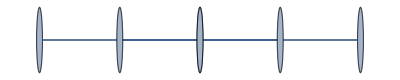

```mathematica
GraphProduct[PathGraph[{1,2}],PathGraph[{1,2,3}],"Cartesian"]
```

bug(425318): GraphProduct could give nice (nondegenerate) embeddings

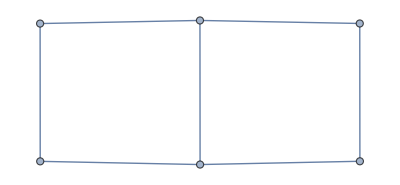

```mathematica
Graph@EdgeList[%]
```

### Adjacency matrices

Hammack et al. (2016)

```mathematica
With[{G=PathGraph[{1,2}],H=PathGraph[{1,2,3}]},
IsomorphicGraphQ[
GraphProduct[G,H,"Cartesian"],
AdjacencyGraph[KroneckerProduct[AdjacencyMatrix[G],IdentityMatrix[VertexCount[H]]]+KroneckerProduct[IdentityMatrix[VertexCount[G]],AdjacencyMatrix[H]]]
]]
```

True

## Timings

bug(413615): GraphComputation`GraphProduct[_, _, "Cartesian"] slowdown in V13

### V12.2

```mathematica
$Version
```

12.2.0 for Mac OS X x86 (64-bit) (December 12, 2020)

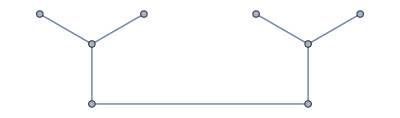

```mathematica
g1=CompleteGraph[2];
g2=GraphData[{"Firecracker",{2,4}}]
```

```mathematica
RepeatedTiming[GraphComputation`GraphProduct[g1,g2,"Cartesian"]]//First
```

0.000379551

```mathematica
Length[gsv122=GraphData[{"Connected","UnitDistance"},;;100]]
```

1529

```mathematica
gsv122={};
```

```mathematica
data122=Monitor[{g=#,Timing[GraphComputation`GraphProduct[CompleteGraph[2],GraphData[#],"Cartesian"]][[1]]}&/@gsv122,g];//Timing
```

{10.5972,Null}

```mathematica
data122={};
```

### V13.0

```mathematica
$Version
```

13.0.0 for Mac OS X x86 (64-bit) (August 21, 2021)

```mathematica
g1=CompleteGraph[2];
g2=GraphData[{"Firecracker",{2,4}}]
```

-Graphics-

```mathematica
RepeatedTiming[GraphComputation`GraphProduct[g1,g2,"Cartesian"]]//First
```

0.00107425

```mathematica
0.001074248046875/0.00037955078125
```

2.83031

```mathematica
Length[gsv130=GraphData[{"Connected","UnitDistance"},;;100]]
```

4751

```mathematica
data130=Monitor[{g=#,Timing[GraphComputation`GraphProduct[CompleteGraph[2],GraphData[#],"Cartesian"]][[1]]}&/@gsv130,g];//Timing
```

{150.654,Null}

```mathematica
Take[data122,2]
```

{{6,16},{6,21}}

### Both

```mathematica
Complement[gsv122,gsv130]
```

{Butane,Decane,Ethane,Heptane,Hexane,Isobutane,Nonane,Octane,Pentane,Propane,{6,125},{7,489},{7,780},{BlackBishop,{3,4}},{BlackBishop,{3,5}},{BracedOctagon,{56,1}},{Cubic,{8,2}},{Cubic,{10,6}},{Cubic,{10,7}},{Cubic,{10,12}},{Cubic,{12,29}},{Fusene,{2,1}},{Fusene,{3,1}},{Fusene,{3,3}},{Fusene,{4,1}},{Fusene,{4,2}},{QuasiCubic,{9,7}},{QuasiCubic,{9,9}},{QuasiCubic,{9,25}},{UnitDistance,{21,2}}}

```mathematica
Complement[gsv130,gsv122]
```

{AntilogGraph,ArayaWienerGraph70,ArayaWienerGraph88,Balaban10Cage,BarnetteBosakLederbergGraph,CelminsSwartSnark1,CelminsSwartSnark2,CisSquareWithTwoTriangles,ConcertinaGraph,CrossingNumberGraph10A,CrossingNumberGraph10B,CrossingNumberGraph12A,CrossingNumberGraph3D,CrossingNumberGraph5B,3224,{Cage,{3,9},5},{Cage,{3,9},6},{Cage,{3,9},7},{Cage,{3,9},8},{Cage,{3,9},9},{Cage,{3,9},10},{Cage,{3,9},11},{Cage,{3,9},12},{Cage,{3,9},13},{Cage,{3,9},14},{Cage,{3,9},15},{Cage,{3,9},16},{Cage,{3,9},17},{Cage,{3,9},18}}
 |  |  |  |

```mathematica
Length[gs=Intersection[gsv130,gsv122]]
```

1499

```mathematica
ratios=Reverse@SortBy[{#1[[1]],#2[[3]]/#1[[3]]}&@@@Select[SplitBy[Sort[Join[{#,1,#2}&@@@data122,{#,2,#2}&@@@data130]],First],Length[#]==2&],Last];
```

```mathematica
Take[ratios,3]
```

{{{Firecracker,{2,4}},54.7303},{{Firecracker,{3,3}},54.0045},{{UniquelyPancyclic,{14,2}},52.6976}}

```mathematica
ListPlot[Callout[#2,#1]&@@@Take[ratios,100]]
```

-Graphics-

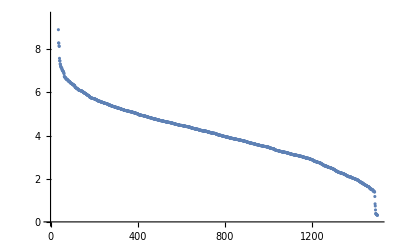

```mathematica
ListPlot[#2&@@@ratios]
```

## Search

```mathematica
$Version
```

13.1.0 for Mac OS X x86 (64-bit) (June 16, 2022)

```mathematica
Length[ud100=GraphData[{"UnitDistance","Connected"},;;100]]
```

4793

```mathematica
Length[ud1000=GraphData[{"UnitDistance","Connected"},;;1000]]
```

5244

### DiamondGraph□G

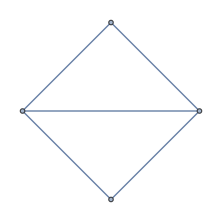

```mathematica
GraphData["DiamondGraph"]
```

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[GraphData["DiamondGraph"],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{90.3207,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[GraphData["DiamondGraph"],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{891.512,{}}

### GemGraph□G

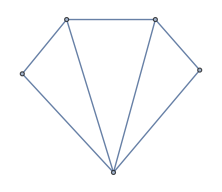

```mathematica
GraphData["GemGraph"]
```

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[GraphData["GemGraph"],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{88.7435,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[GraphData["GemGraph"],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{1029.51,{}}

### C_3□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[CycleGraph[3],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{140.601,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[CycleGraph[3],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{1018.77,{}}

### C_4□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[CycleGraph[4],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{148.334,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[CycleGraph[4],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{1135.15,{}}

### C_5□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[CycleGraph[5],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{147.155,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[CycleGraph[5],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{1176.19,{}}

### P_2□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[CompleteGraph[2],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{137.253,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[CompleteGraph[2],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{741.856,{}}

### P_3□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[PathGraph[Range[3]],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{131.435,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[PathGraph[Range[3]],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{1094.59,{}}

### P_4□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[PathGraph[Range[4]],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{134.503,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[PathGraph[Range[4]],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{1207.33,{}}

### Q_3□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[HypercubeGraph[3],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{1415.37,{}}

### Q_4□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[HypercubeGraph[4],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{1807.2,{}}

### S_3□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[StarGraph[3],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{176.391,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[StarGraph[3],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{883.682,{}}

### S_4□G

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[StarGraph[4],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud100,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{193.83,{}}

```mathematica
Monitor[Select[DeleteCases[{gn=#,RecognizeGraph[GraphCartesianProduct[StarGraph[4],GraphData[#]],"Cache"->"InternalOnly"]}&/@Take[ud1000,All],{_,{}}],GraphData[#[[2]],"UnitDistance"]=!=True&],gn]//Timing
```

{945.261,{}}

## Embeddings

```mathematica
<<MathWorld`Graphs`
```

### "GraphCartesianProductOfK33AndK3"

#### Names

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","StandardName"]
```

GraphCartesianProductOfK33AndK3

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","StandardNames"]
```

{GraphCartesianProductOfK33AndK3,{VertexTransitive,{18,38}}}

#### Primary

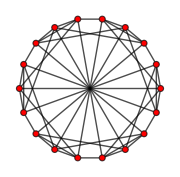

```mathematica
GraphData["GraphCartesianProductOfK33AndK3"]//StyleGraphs[#,ImageSize->Small]&
```

#### All

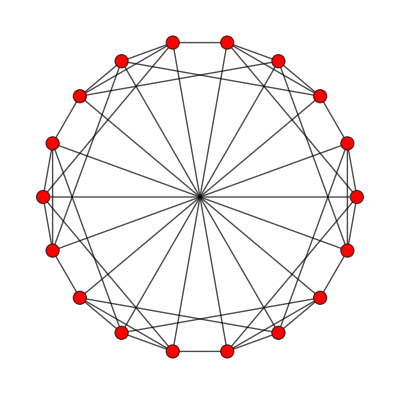
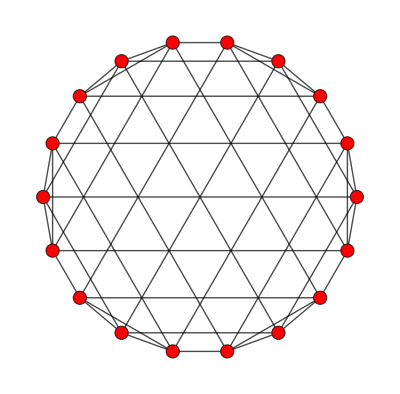
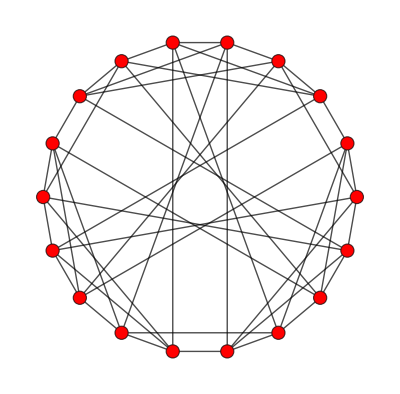
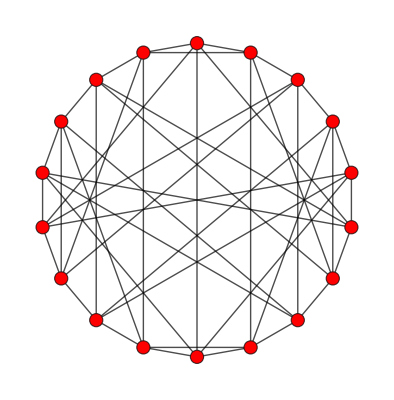
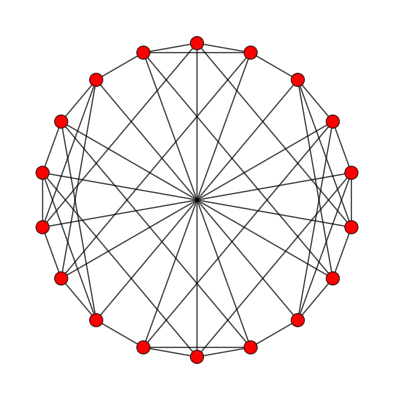
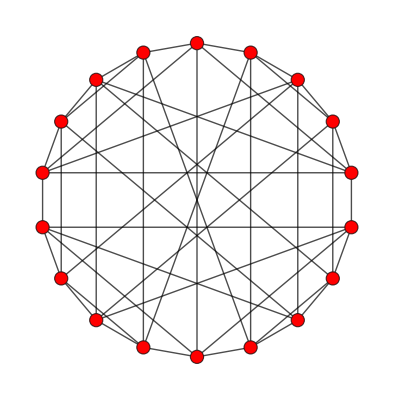
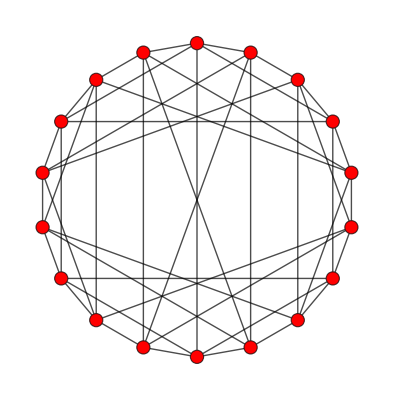
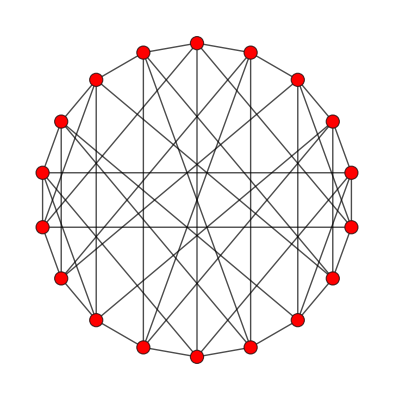

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","All"]//StyleGraphs
```

#### Inexact

```mathematica
Select[GraphData["GraphCartesianProductOfK33AndK3","Graph","All"],(!FreeQ[GraphEmbedding[#],_?InexactNumberQ]&)]//StyleGraphs
```

{}

#### Embedding types

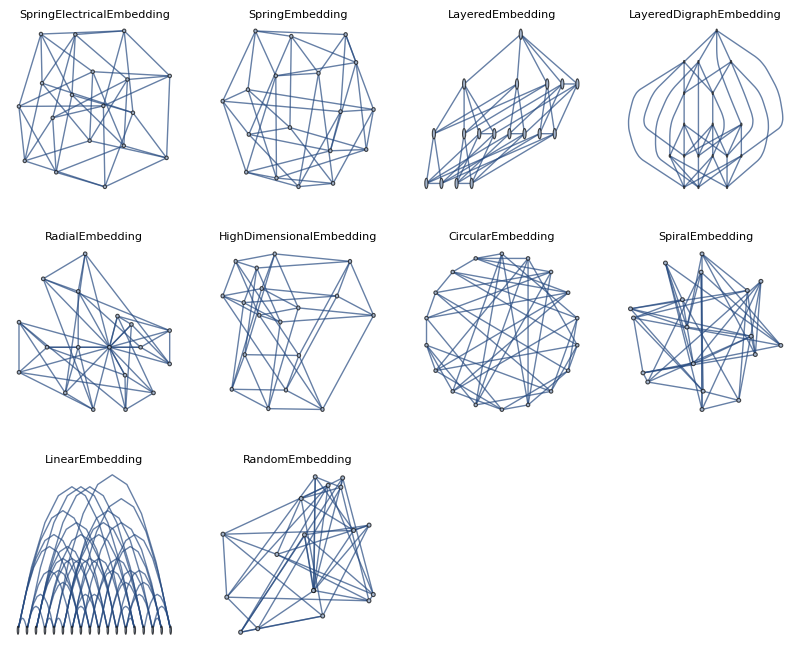

```mathematica
GraphDataEmbeddings[GraphData["GraphCartesianProductOfK33AndK3","EdgeList"]]
```

#### Default embedding

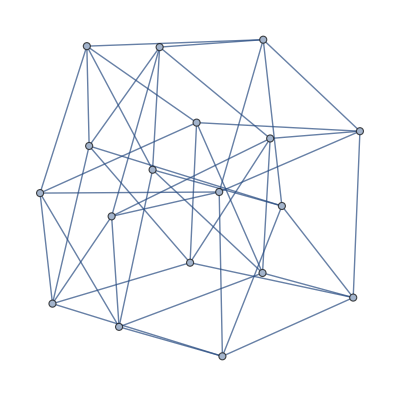

```mathematica
GraphPlot@GraphData["GraphCartesianProductOfK33AndK3","Edges"]
```

```mathematica
v={};
g=Graph[Range[Length[v]],UndirectedEdge@@@{},VertexCoordinates->v,VertexLabels->Automatic]
```

```mathematica
RecognizeGraph[g]
```

#### Degenerate

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Degenerate"]//StyleGraphs
```

{}

```mathematica
DegenerateGraphEmbeddingTypes/@GraphData["GraphCartesianProductOfK33AndK3","Graph","Degenerate"]
```

{}

#### Bilateral

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Bilateral"]//StyleGraphs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Circular

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Circular"]//StyleGraphs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Planar

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Planar"]
```

False

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Planar"]//StyleGraphs
```

{}

#### MinimalCrossing

```mathematica
GraphData["GraphCartesianProductOfK33AndK3",{"RCN","CN"}]
```

{Missing[NotAvailable],25}

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","MinimalCrossing"]//StyleGraphs
```

{}

#### MinimalCrossing construction

```mathematica
(cn=CrossingNumber[GraphData["GraphCartesianProductOfK33AndK3"],TimeConstraint->1])//AbsoluteTiming
```

{1.16818,25}

```mathematica
(cn=CrossingNumber[GraphData["GraphCartesianProductOfK33AndK3"],TimeConstraint->10])//AbsoluteTiming
```

```mathematica
(g=MinimalCrossingGraph[GraphData["GraphCartesianProductOfK33AndK3"],"CrossingNumber"->cn])//PolyhedralGraphQ
```

True

```mathematica
faces=ReverseSort@SymmetricallyDistinctFaces[g]
```

{{37,42,41,38},{20,21,32,43},{17,32,21,22},{15,43,32,31},{15,24,23,43},{13,23,24,18},{12,41,42,39},{10,40,14,35},{10,36,37,40},{9,29,28,11},{9,11,38,41},{8,40,37,38},{7,39,42,36},{7,13,18,39},{7,10,16,25},{6,30,9,12},{6,24,15,34},{5,27,28,33},{4,35,14,26},{4,26,22,21},{4,21,20,19},{3,33,28,29},{3,31,17,33},{3,29,30,34},{2,8,11,27},{2,5,22,26},{1,25,16,19},{1,20,43,23},{36,42,37},{17,31,32},{12,39,18},{11,28,27},{10,35,16},{9,41,12},{9,30,29},{8,38,11},{8,14,40},{7,36,10},{7,25,13},{6,34,30},{6,18,24},{6,12,18},{5,33,17},{5,17,22},{4,19,16},{4,16,35},{3,34,15},{3,15,31},{2,27,5},{2,26,14},{2,14,8},{1,23,13},{1,19,20},{1,13,25}}

```mathematica
Tally[ReverseSort[Length/@faces]]
```

{{4,28},{3,26}}

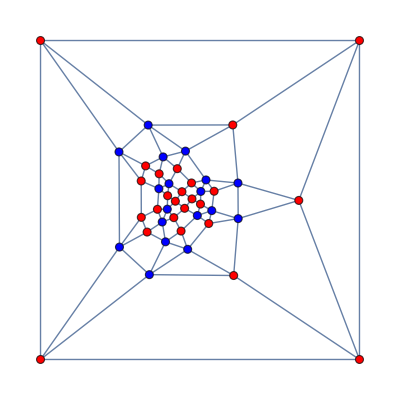
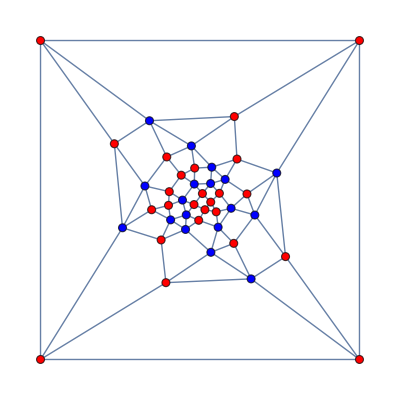
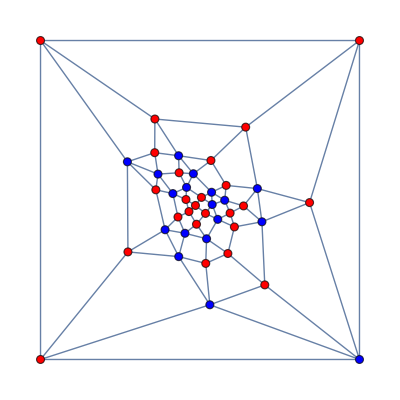
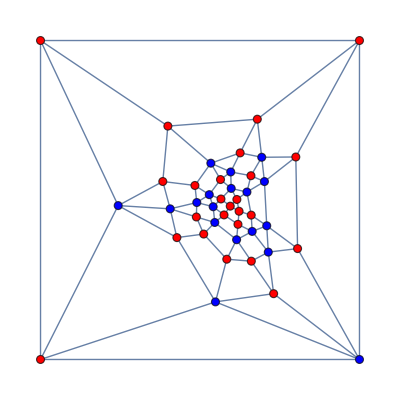
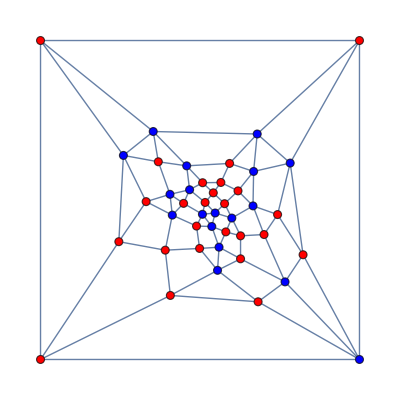
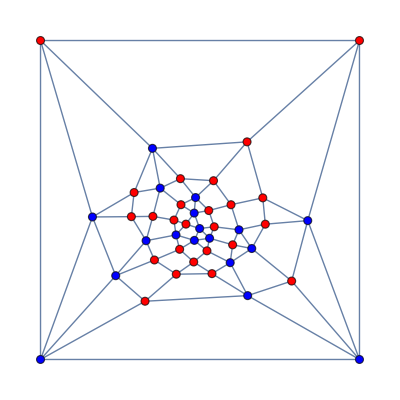
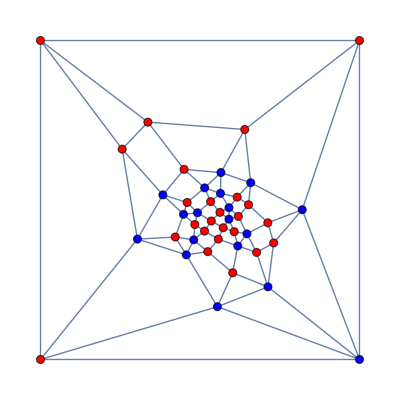
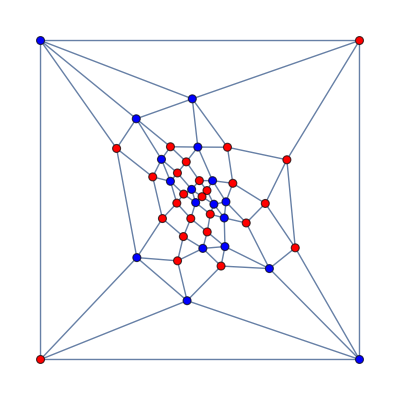

```mathematica
IGLayoutTutte[g,"OuterFace"->#]&/@faces
```

```mathematica
Union[Select[Table[RotateGraph[MinimalCrossingGraph[GraphData["GraphCartesianProductOfK33AndK3"],"CrossingNumber"->cn,RandomSeed->n]],{n,50}],Max[OuterFace[#]]<=GraphData["GraphCartesianProductOfK33AndK3","V"]&]]//Timing
```

{2.41923,{}}

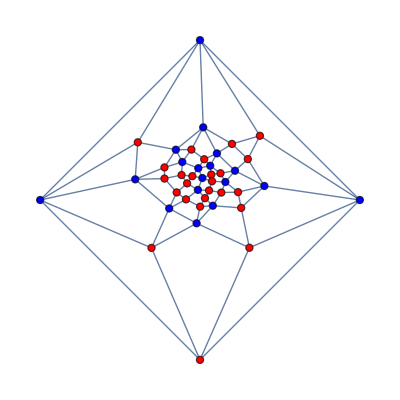
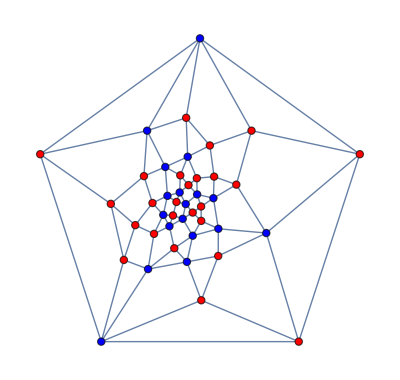
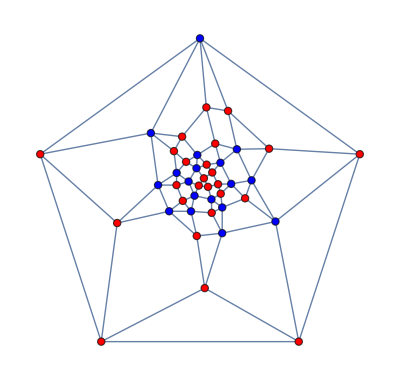
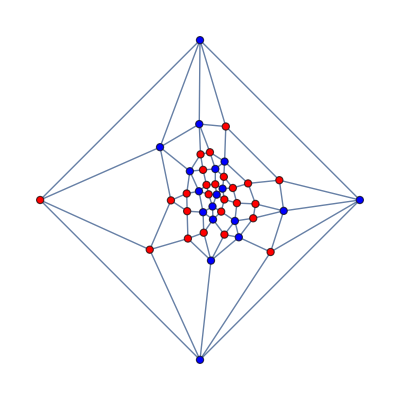
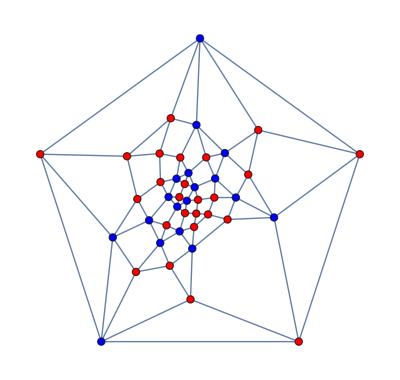
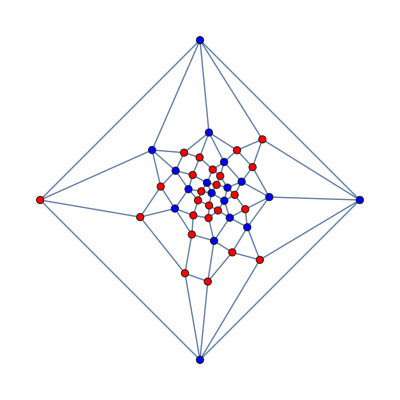
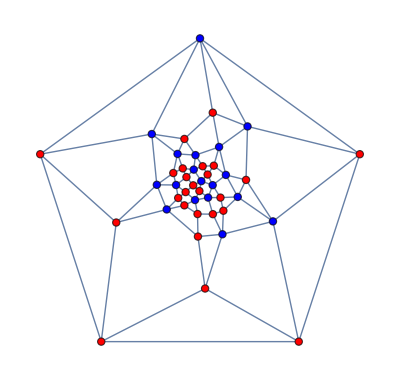
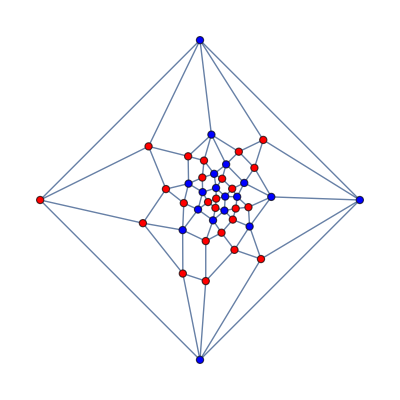
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MinimalCrossingGraph[GraphData["GraphCartesianProductOfK33AndK3"],"CrossingNumber"->cn,RandomSeed->i],{i,50}]//Union
```

```mathematica
v={};
g=Graph[Range[Length[v]],UndirectedEdge@@@{},VertexCoordinates->v,VertexLabels->Automatic]
```

```mathematica
RecognizeGraph[g]
```

```mathematica
RectilinearCrossingCount[g]
```

#### Circulant

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Circulant"]
```

False

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Circulant"]//StyleGraphs
```

{}

#### Line graph

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Line"]
```

False

```mathematica
LineGraphQ[GraphData["GraphCartesianProductOfK33AndK3"]]//Timing
```

{0.001119,False}

#### RootGraph

```mathematica
Select[GraphData[All],GraphData[#,"LineGraph","Name"]=== "GraphCartesianProductOfK33AndK3"&]
```

{}

```mathematica
RootGraph[GraphData["GraphCartesianProductOfK33AndK3"]]
```

Failure[-Graphics-,<|MessageTemplate→Graph is not a line graph|>]

#### Halin

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Halin"]
```

False

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Halin"]//StyleGraphs
```

{}

#### Rigid

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Rigid"]
```

True

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Rigid"]//StyleGraphs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Flexible

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Flexible"]
```

False

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Flexible"]//StyleGraphs
```

{}

#### LCF

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","LCF"]
```

True

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","HamiltonianCycleCount"]
```

68616

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","LCFSignature"]
```

{{6,2},{3,1},{2,14},{1,310}}

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","LCFNotations"]
```

Missing[TooLarge,{{{{-9,-4,-2},{-9,2,4},{-9,-4,4}},6},{{{-9,-3,3},{-5,-2,7},{-7,2,5}},6},{{{-8,-4,-3},{3,4,8},{-3,4,8},{-8,3,8},{-8,-3,8},{-8,-4,3}},3},{{{-9,-7,-5},{-8,-5,-3},{-5,7,8},{-7,-5,2},{-9,-5,5},{-2,5,7},{-8,-7,5},{3,5,8},{-9,5,7}},2},{{{-9,-7,-4},{-9,-4,-3},{-9,2,7},{-9,-5,5},{-9,-7,-2},{-9,3,4},{-9,4,7},{-9,3,5},{-9,-5,-3}},2},{{{-9,-7,-4},{-9,-4,-3},{-9,2,7},{-8,-6,5},{-6,-2,8},{-6,3,4},{-8,4,6},{3,6,8},{-5,-3,6}},2},{{{-9,-7,-2},{-9,-5,-4},{-9,-7,7},{-8,-6,5},{-6,7,8},{-8,3,5},{4,6,8},{-8,2,6},{-5,-3,8}},2},{{{-9,-7,-2},{-9,-4,4},{-9,2,7},{-8,-6,5},{-2,3,8},{-8,-6,-4},{4,6,8},{-8,-3,2},{-5,6,8}},2},{{{-9,-7,-2},{-9,3,4},{-9,4,7},{-6,3,5},{-8,-6,-3},{-6,-4,8},{-4,-3,6},{-8,2,6},{-5,6,8}},2},{{{-9,-7,5},{-9,-3,3},{-9,-5,7},{-6,3,5},{-6,-3,3},{-6,-5,3},{-3,5,6},{-3,3,6},{-5,-3,6}},2},{{{-9,-7,5},{-9,-3,5},{-9,-7,7},{-8,3,5},{3,7,8},{-6,-5,3},{-8,-5,-3},{-3,3,8},{-5,-3,6}},2},{{{-9,-7,5},{-8,-3,3},{-5,7,8},{-5,4,5},{-7,-3,2},{-9,-5,3},{-2,5,7},{-4,3,5},{-9,-5,-3}},2},{{{-9,-7,7},{-9,-5,3},{-9,-5,7},{-6,3,5},{-8,-3,3},{3,5,8},{-3,5,6},{-8,-7,-3},{-5,-3,8}},2},{{{-9,-7,7},{-9,-5,5},{-9,-7,7},{-8,3,5},{3,7,8},{-8,3,5},{-5,-3,8},{-8,-7,-3},{-5,-3,8}},2},{{{-9,-7,7},{-9,4,5},{-9,2,7},{-8,3,5},{-6,-2,8},{-8,-6,-4},{-5,-3,8},{-8,-7,6},{-5,6,8}},2},{{{-9,-5,7},{-9,3,5},{-5,-3,4},{-7,-5,2},{-9,-3,5},{-2,3,7},{-5,-4,5},{-8,-7,5},{-3,3,8}},2},{{{-9,-4,-2},{-9,2,4},{-8,-3,4},{-5,-2,8},{-7,2,4},{-9,-4,4},{-4,-2,7},{-8,2,5},{-4,3,8}},2}}]

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","LCF"]//StyleGraphs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Tally[LCFNotation[#][[2]]&/@%]
```

{{6,2},{3,1},{2,14}}

#### LCF compute all

```mathematica
Length[FindHamiltonianCycle[GraphData["GraphCartesianProductOfK33AndK3"],All][[All,All,1]]]//Timing
```

{0.217953,68616}

```mathematica
Tally[(lcf=LCF[GraphData["GraphCartesianProductOfK33AndK3"],All])[[All,2]]]//Timing
```

{8.54685,{{6,2},{3,1},{2,14},{1,310}}}

```mathematica
DeleteCases[lcf,{_,1}]
```

{{{{-9,-4,-2},{-9,2,4},{-9,-4,4}},6},{{{-9,-3,3},{-5,-2,7},{-7,2,5}},6},{{{-8,-4,-3},{3,4,8},{-3,4,8},{-8,3,8},{-8,-3,8},{-8,-4,3}},3},{{{-9,-7,-5},{-8,-5,-3},{-5,7,8},{-7,-5,2},{-9,-5,5},{-2,5,7},{-8,-7,5},{3,5,8},{-9,5,7}},2},{{{-9,-7,-4},{-9,-4,-3},{-9,2,7},{-9,-5,5},{-9,-7,-2},{-9,3,4},{-9,4,7},{-9,3,5},{-9,-5,-3}},2},{{{-9,-7,-4},{-9,-4,-3},{-9,2,7},{-8,-6,5},{-6,-2,8},{-6,3,4},{-8,4,6},{3,6,8},{-5,-3,6}},2},{{{-9,-7,-2},{-9,-5,-4},{-9,-7,7},{-8,-6,5},{-6,7,8},{-8,3,5},{4,6,8},{-8,2,6},{-5,-3,8}},2},{{{-9,-7,-2},{-9,-4,4},{-9,2,7},{-8,-6,5},{-2,3,8},{-8,-6,-4},{4,6,8},{-8,-3,2},{-5,6,8}},2},{{{-9,-7,-2},{-9,3,4},{-9,4,7},{-6,3,5},{-8,-6,-3},{-6,-4,8},{-4,-3,6},{-8,2,6},{-5,6,8}},2},{{{-9,-7,5},{-9,-3,3},{-9,-5,7},{-6,3,5},{-6,-3,3},{-6,-5,3},{-3,5,6},{-3,3,6},{-5,-3,6}},2},{{{-9,-7,5},{-9,-3,5},{-9,-7,7},{-8,3,5},{3,7,8},{-6,-5,3},{-8,-5,-3},{-3,3,8},{-5,-3,6}},2},{{{-9,-7,5},{-8,-3,3},{-5,7,8},{-5,4,5},{-7,-3,2},{-9,-5,3},{-2,5,7},{-4,3,5},{-9,-5,-3}},2},{{{-9,-7,7},{-9,-5,3},{-9,-5,7},{-6,3,5},{-8,-3,3},{3,5,8},{-3,5,6},{-8,-7,-3},{-5,-3,8}},2},{{{-9,-7,7},{-9,-5,5},{-9,-7,7},{-8,3,5},{3,7,8},{-8,3,5},{-5,-3,8},{-8,-7,-3},{-5,-3,8}},2},{{{-9,-7,7},{-9,4,5},{-9,2,7},{-8,3,5},{-6,-2,8},{-8,-6,-4},{-5,-3,8},{-8,-7,6},{-5,6,8}},2},{{{-9,-5,7},{-9,3,5},{-5,-3,4},{-7,-5,2},{-9,-3,5},{-2,3,7},{-5,-4,5},{-8,-7,5},{-3,3,8}},2},{{{-9,-4,-2},{-9,2,4},{-8,-3,4},{-5,-2,8},{-7,2,4},{-9,-4,4},{-4,-2,7},{-8,2,5},{-4,3,8}},2}}

```mathematica
LCFGraph@@@DeleteCases[lcf,{_,1}]//StyleGraphs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(gs=Flatten[{
(* all LCF's with order >1, sorted by order and with bilateral graphs first *)
Join[DeleteCases[#,{_Missing,_}][[All,1]],Cases[#,{_Missing,_}][[All,2]]]&/@Map[{BilateralLCFGraph@#,#}&,Map[LCFGraph@@#&,SplitBy[DeleteCases[lcf,{_,1}],Last],{2}],{2}],
(* order-1 bilateral only *)
DeleteMissing[BilateralLCFGraph@@@Cases[lcf,{_,1}]]}])//Timing
```

{10.4824,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Length[gs]
```

65

```mathematica
(gs=Flatten[{
(* all LCF's with order >1, sorted by order and with bilateral graphs first *)
Join[DeleteCases[#,{_Missing,_}][[All,1]],Cases[#,{_Missing,_}][[All,2]]]&/@Map[{BilateralLCFGraph@#,#}&,Map[LCFGraph@@#&,SplitBy[DeleteCases[lcf,{_,1}],Last],{2}],{2}],
(* order-1 bilateral only *)
DeleteMissing[BilateralLCFGraph@@@Cases[lcf,{_,XXX}]]}])//Timing
```

{0.446299,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Length[gs]
```

17

#### UnitDistance

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","UnitDistance"]
```

False

```mathematica
UnitDistanceGraphQ[GraphData["GraphCartesianProductOfK33AndK3"],Debug->True]//Timing
```

Skipping computation and checking of blocks

Checking presence of unit-distance forbidden graphs...

Graph contains unit-distance forbidden graph {CompleteBipartite,{2,3}}

{0.022289,False}

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","UnitDistance"]//StyleGraphs
```

{}

```mathematica
Select[%,!FreeQ[GraphEmbedding[#],_?InexactNumberQ]&]
```

{}

#### UnitDistance by refinement

```mathematica
UnitDistanceEmbeddingRefine[Graph[GraphData["GraphCartesianProductOfK33AndK3","VertexList"],GraphData["GraphCartesianProductOfK33AndK3","EdgeList"]],MaxIterations->500]
```

-Graphics-

```mathematica
UnitDistanceEmbeddingRefine[Annotate[#,VertexCoordinates->N[GraphEmbedding[#]]],MaxIterations->500]&/@Complement@@(GraphData["GraphCartesianProductOfK33AndK3","Graph",#]&/@{"All","UnitDistance"})
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### UnitDistance by FindUnitDistanceEmbedding

```mathematica
FindUnitDistanceEmbedding[GraphData["GraphCartesianProductOfK33AndK3"],MaxIterations->5000,"ReturnWithMessage"->True]//Timing
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Message generated; returning

{0.738216,-Graphics-}

#### Matchstick

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Matchstick"]
```

False

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph","Matchstick"]//StyleGraphs
```

{}

#### 3D default

```mathematica
Graph3D[GraphData["GraphCartesianProductOfK33AndK3","Edges"]]
```

-Graphics3D-

#### 3D All

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph",{"3D","All"}]
```

{}

#### 3D UnitDistance

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph",{"3D","UnitDistance"}]
```

{}

#### 3D Polyhedron

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Polyhedral"]
```

False

```mathematica
GraphData["GraphCartesianProductOfK33AndK3","Graph",{"3D","Polyhedron"}]
```

{}